```mathematica
ClearAll["Global`*"];
interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_full/Dirs_kIUnbind_DT_2/fac_List[1.0,0]/sol.mx"];
(*interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_diffs/fac_1.0/sol.mx"];*)
```

```mathematica
CDISol = interpList[[1]];
CDASol = interpList[[2]];
CBISol = interpList[[3]];
CBASol = interpList[[4]];
CCSol = interpList[[5]];
CDSol = interpList[[6]];
CDstSol = interpList[[7]];
uxSol = interpList[[8]];
uySol = interpList[[9]];
vxSol[x_,y_,t_]:=Evaluate[D[uxSol[x,y,tp],tp]/.tp->t];
vySol[x_,y_,t_]:=Evaluate[D[uySol[x,y,tp],tp]/.tp->t];

xMax = 300;
yMax = 300;
tMax = 150;

width = 2.5;
r0 = 75;
cyc = 20;
len=5;
del=0.75;


(*import functions*)
Get["/Users/csfloyd/Dropbox/Projects/TCB2Network/Mathematica/MidwayFiles/src/TCB2Functions.m"]
```

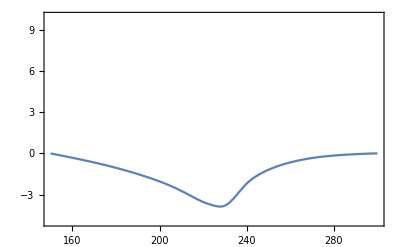

```mathematica
Plot[uxSol[x,xMax/2,130],{x,xMax/2,xMax},PlotRange->{-5,10}]
```

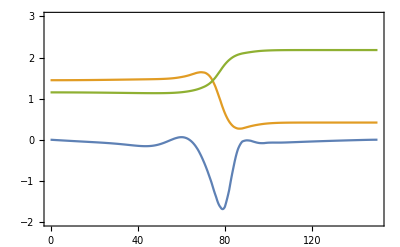

```mathematica
tpp=140;
off = 150;
paa = Plot[{10*vxSol[x+off,xMax/2,tpp],CBISol[x+off,xMax/2,tpp]+CBASol[x+off,xMax/2,tpp],CDISol[x+off,xMax/2,tpp]+CDASol[x+off,xMax/2,tpp]},{x,0,xMax/2},PlotRange->{-2,3}]
```

```mathematica
Manipulate[Plot[uxSol[x,xMax/2,t],{x,0,xMax},PlotRange->{-5,10}],{t,0,tMax}]
```

Plot::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

```mathematica
pList = {};
Do[
p = Plot3D[gamFunc[x,y,t],{x,0,xMax},{y,0,yMax},PlotPoints->100,PlotRange->{0,1},AxesLabel->{"x (μm)","y (μm)","γ"}];
AppendTo[pList,p];
,{t,0,tMax}]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Movies/gamma.mp4",pList];
```

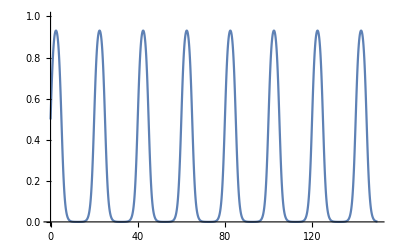

```mathematica
pos[Ri_,t_,f_]:=Ri + f*{uxSol[Ri[[1]],Ri[[2]],t],uySol[Ri[[1]],Ri[[2]],t]};
pA[CBA_,CBI_]:=CBA/(CBA+CBI);
divV[x_,y_,t_]:=Evaluate[D[vxSol[xp,y,t],xp]+D[vySol[x,yp,t],yp]/.{xp->x,yp->y}];
curlV[x_,y_,t_]:=Evaluate[D[vySol[xp,y,t],xp]-D[vxSol[x,yp,t],yp]/.{xp->x,yp->y}];

divU[x_,y_,t_]:=Evaluate[D[uxSol[xp,y,t],xp]+D[uySol[x,yp,t],yp]/.{xp->x,yp->y}];
curlU[x_,y_,t_]:=Evaluate[D[uySol[xp,y,t],xp]-D[uxSol[x,yp,t],yp]/.{xp->x,yp->y}];

fac = 50;

Ris = Flatten[Table[{i,j},{i,0,xMax,xMax/fac},{j,0,yMax,yMax/fac}],1];
funcArray[t_]:=Table[{pos[Ris[[i]],t,5]},{i,1,Length[Ris]}]
sizeArray[t_]:=0.2*10^-2 Table[CBASol[Ris[[i]][[1]],Ris[[i]][[2]],t]+CBISol[Ris[[i]][[1]],Ris[[i]][[2]],t],{i,1,Length[Ris]}];

sigmoid[x_]:=1/(1+Exp[-x]);
smoothBump[x_,a_,xa_,xb_]:=sigmoid[(x-xa)/a]-sigmoid[(x-xb)/a]
waveFunc[t_,cyc_,len_,del_]:=Sum[smoothBump[t,del,cyc*i,cyc*i+len],{i,0,Floor[tMax/cyc]}];
Plot[waveFunc[t,cyc,len,del],{t,0,tMax},PlotRange->{0,1}]
Manipulate[Plot[waveFunc[t,cyc,len,del],{t,0,tMax},PlotRange->{0,1}],{cyc,1,40}]
```

```mathematica
Manipulate[Plot[{curlU[xMax/2+0,y,t],divU[xMax/2+0,y,t]},{y,0,xMax},PlotRange->{-1,1}],{t,0,tMax}]
```

Plot::plln: Limiting value xMax in {y,0,xMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{curlV[xMax/2+10,y,t],divV[xMax/2+10,y,t]},{y,0,xMax},PlotRange->{-0.1,0.1}],{t,0,tMax}]
```

Plot::plln: Limiting value xMax in {y,0,xMax} is not a machine-sized real number.

```mathematica
cf=ColorData["LightTemperatureMap"][#]&;

ul = 3;
tMax = 150;
Manipulate[
Plot3D[{curlV[x,y,t],divV[x,y,t]},{x,0,xMax},{y,0,yMax},
PlotRange->{-0.1,0.1},
PlotPoints->150,
ImageSize->800]
,{t,0,tMax}]
```

Plot3D::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

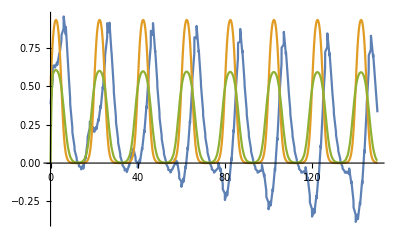

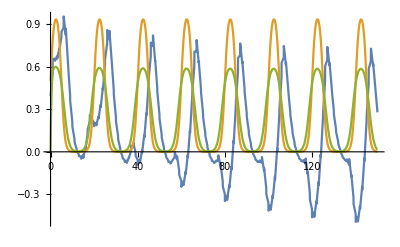

```mathematica
Plot[{5*vxSol[xMax/2+r0,yMax/2,t], waveFunc[t,cyc,len,del], pA[CBASol[xMax/2+r0,yMax/2,t],CBISol[xMax/2+r0,yMax/2,t]]},{t,0,tMax}]
```

```mathematica
SetOptions[DensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

cf=ColorData["LightTemperatureMap"][#]&;

ul = 3;
tMax = 150;

gList = List[];
Do[
g = Show[
DensityPlot[(*pA[CBASol[x,y,t],CBISol[x,y,t]]*)CBASol[x,y,t],{x,0,xMax},{y,0,yMax},
PlotRange->{-0.1,ul},
PlotPoints->150,
ImageSize->800,
PlotLegends->Placed[BarLegend[{cf,{-0.,ul}}],Right],
Axes->False,
ColorFunction->cf,
(*ColorFunctionScaling->False,*)
FrameLabel->{"x (μm)","y (μm)"}],

ListPlot[funcArray[t],AspectRatio->1,PlotRange->{{-1,xMax+1},{-1,yMax+1}},
BaseStyle->Black,
PlotStyle->(PointSize/@( sizeArray[t]))],

Graphics[{EdgeForm[{Thickness[0.008],Opacity[waveFunc[t,cyc,len,del]],Darker@Green}],FaceForm[{Opacity[0.5*waveFunc[t,cyc,len,del]],Darker@Green}],Disk[{xMax/2,yMax/2},r0]}]
(*
VectorPlot[{vxSol[x,y,t],vySol[x,y,t]},{x,0,xMax},{y,0,yMax},VectorColorFunction->None,VectorPoints->Fine,VectorStyle->Black,VectorScaling->Automatic]*)

];

AppendTo[gList, g]

,{t,0,tMax}];
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Movies/BaseCase.mp4",gList];
```